```mathematica
m[R_]:=-(η+ϵ-ϵ*R)+√((η+ϵ-ϵ*R)^2+4*R*ϵ*η)
```

```mathematica
n[R_]:=(((m[R]^2+4η*m[R]+2*ϵ*m[R]+4η^2+4*ϵ*η+4η)^2-4*(2*m[R]^3+12*η*m[R]^2+24*η^2*m[R]+8*ϵ*η*m[R]+16*η^3+16*ϵ*η^2)))/4(m[R]+2η)
```

```mathematica
ϵ=0.5
```

0.5

```mathematica
R=4.5
```

4.5

```mathematica
η=1
```

1

```mathematica
Clear[R,ϵ,η]
```

```mathematica
Solve[n[R]==0,R]
```

{{R→-2. (-1.125+1. η)-0.5 √(16. (-1.125+1. η)^2-24. (0.677083-1.5 η+1. η^2)+0.0833333 (65.-144. η+96. η^2)+(0.00694444 (289.-19968. η+20736. η^2))/(2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3)+(2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3))-0.5 √(32. (-1.125+1. η)^2-24. (0.677083-1.5 η+1. η^2)-0.0833333 (65.-144. η+96. η^2)-(0.00694444 (289.-19968. η+20736. η^2))/(2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3)-1. (2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3)-(0.25 (-512. (-1.125+1. η)^3+768. (-1.125+1. η) (0.677083-1.5 η+1. η^2)-256. (-0.3125-0.3125 η-1.125 η^2+1. η^3)))/(√(16. (-1.125+1. η)^2-24. (0.677083-1.5 η+1. η^2)+0.0833333 (65.-144. η+96. η^2)+(0.00694444 (289.-19968. η+20736. η^2))/(2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3)+(2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3))))},{R→-2. (-1.125+1. η)-0.5 √(16. (-1.125+1. η)^2-24. (0.677083-1.5 η+1. η^2)+0.0833333 (65.-144. η+96. η^2)+(0.00694444 (289.-19968. η+20736. η^2))/(2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3)+(2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3))+0.5 √(32. (-1.125+1. η)^2-24. (0.677083-1.5 η+1. η^2)-0.0833333 (65.-144. η+96. η^2)-(0.00694444 (289.-19968. η+20736. η^2))/(2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3)-1. (2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3)-(0.25 (-512. (-1.125+1. η)^3+768. (-1.125+1. η) (0.677083-1.5 η+1. η^2)-256. (-0.3125-0.3125 η-1.125 η^2+1. η^3)))/(√(16. (-1.125+1. η)^2-24. (0.677083-1.5 η+1. η^2)+0.0833333 (65.-144. η+96. η^2)+(0.00694444 (289.-19968. η+20736. η^2))/(2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3)+(2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3))))},{R→-2. (-1.125+1. η)+0.5 √(16. (-1.125+1. η)^2-24. (0.677083-1.5 η+1. η^2)+0.0833333 (65.-144. η+96. η^2)+(0.00694444 (289.-19968. η+20736. η^2))/(2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3)+(2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3))-0.5 √(32. (-1.125+1. η)^2-24. (0.677083-1.5 η+1. η^2)-0.0833333 (65.-144. η+96. η^2)-(0.00694444 (289.-19968. η+20736. η^2))/(2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3)-1. (2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3)+(0.25 (-512. (-1.125+1. η)^3+768. (-1.125+1. η) (0.677083-1.5 η+1. η^2)-256. (-0.3125-0.3125 η-1.125 η^2+1. η^3)))/(√(16. (-1.125+1. η)^2-24. (0.677083-1.5 η+1. η^2)+0.0833333 (65.-144. η+96. η^2)+(0.00694444 (289.-19968. η+20736. η^2))/(2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3)+(2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3))))},{R→-2. (-1.125+1. η)+0.5 √(16. (-1.125+1. η)^2-24. (0.677083-1.5 η+1. η^2)+0.0833333 (65.-144. η+96. η^2)+(0.00694444 (289.-19968. η+20736. η^2))/(2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3)+(2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3))+0.5 √(32. (-1.125+1. η)^2-24. (0.677083-1.5 η+1. η^2)-0.0833333 (65.-144. η+96. η^2)-(0.00694444 (289.-19968. η+20736. η^2))/(2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3)-1. (2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3)+(0.25 (-512. (-1.125+1. η)^3+768. (-1.125+1. η) (0.677083-1.5 η+1. η^2)-256. (-0.3125-0.3125 η-1.125 η^2+1. η^3)))/(√(16. (-1.125+1. η)^2-24. (0.677083-1.5 η+1. η^2)+0.0833333 (65.-144. η+96. η^2)+(0.00694444 (289.-19968. η+20736. η^2))/(2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3)+(2.84317-566.667 η+2514. η^2-1728. η^3+0.000289352 √(0.-1.84735×10^10 η+2.60253×10^12 η^2+5.70518×10^11 η^3-1.82671×10^12 η^4-7.43008×10^11 η^5))^(1/3))))}}

```mathematica
p[η_]:=-2. (-1.125+1. η)+0.5 √(16. (-1.125+1. η)^2-24. (0.6770833333333334-1.5 η+1. η^2)+0.08333333333333333 (65.-144. η+96. η^2)+(0.006944444444444444 (289.-19968. η+20736. η^2))/(2.8431712962962963-566.6666666666666 η+2514. η^2-1728. η^3+0.00028935185185185184 √(0.-1.8473508864*^10 η+2.602527473664*^12 η^2+5.7051758592*^11 η^3-1.82670557184*^12 η^4-7.43008370688*^11 η^5))^(1/3)+(2.8431712962962963-566.6666666666666 η+2514. η^2-1728. η^3+0.00028935185185185184 √(0.-1.8473508864*^10 η+2.602527473664*^12 η^2+5.7051758592*^11 η^3-1.82670557184*^12 η^4-7.43008370688*^11 η^5))^(1/3))-0.5 √(32. (-1.125+1. η)^2-24. (0.6770833333333334-1.5 η+1. η^2)-0.08333333333333333 (65.-144. η+96. η^2)-(0.006944444444444444 (289.-19968. η+20736. η^2))/(2.8431712962962963-566.6666666666666 η+2514. η^2-1728. η^3+0.00028935185185185184 √(0.-1.8473508864*^10 η+2.602527473664*^12 η^2+5.7051758592*^11 η^3-1.82670557184*^12 η^4-7.43008370688*^11 η^5))^(1/3)-1. (2.8431712962962963-566.6666666666666 η+2514. η^2-1728. η^3+0.00028935185185185184 √(0.-1.8473508864*^10 η+2.602527473664*^12 η^2+5.7051758592*^11 η^3-1.82670557184*^12 η^4-7.43008370688*^11 η^5))^(1/3)+(0.25 (-512. (-1.125+1. η)^3+768. (-1.125+1. η) (0.6770833333333334-1.5 η+1. η^2)-256. (-0.3125-0.3125 η-1.125 η^2+1. η^3)))/(√(16. (-1.125+1. η)^2-24. (0.6770833333333334-1.5 η+1. η^2)+0.08333333333333333 (65.-144. η+96. η^2)+(0.006944444444444444 (289.-19968. η+20736. η^2))/(2.8431712962962963-566.6666666666666 η+2514. η^2-1728. η^3+0.00028935185185185184 √(0.-1.8473508864*^10 η+2.602527473664*^12 η^2+5.7051758592*^11 η^3-1.82670557184*^12 η^4-7.43008370688*^11 η^5))^(1/3)+(2.8431712962962963-566.6666666666666 η+2514. η^2-1728. η^3+0.00028935185185185184 √(0.-1.8473508864*^10 η+2.602527473664*^12 η^2+5.7051758592*^11 η^3-1.82670557184*^12 η^4-7.43008370688*^11 η^5))^(1/3))))
```

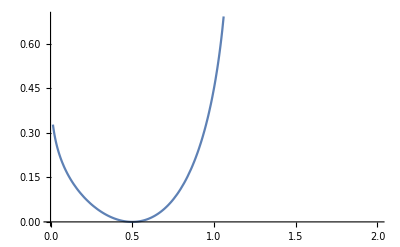

```mathematica
Plot[p[η],{η,0,2}]
```

```mathematica
q[η_]:=-2. (-1.125+1. η)+0.5 √(16. (-1.125+1. η)^2-24. (0.6770833333333334-1.5 η+1. η^2)+0.08333333333333333 (65.-144. η+96. η^2)+(0.006944444444444444 (289.-19968. η+20736. η^2))/(2.8431712962962963-566.6666666666666 η+2514. η^2-1728. η^3+0.00028935185185185184 √(0.-1.8473508864*^10 η+2.602527473664*^12 η^2+5.7051758592*^11 η^3-1.82670557184*^12 η^4-7.43008370688*^11 η^5))^(1/3)+(2.8431712962962963-566.6666666666666 η+2514. η^2-1728. η^3+0.00028935185185185184 √(0.-1.8473508864*^10 η+2.602527473664*^12 η^2+5.7051758592*^11 η^3-1.82670557184*^12 η^4-7.43008370688*^11 η^5))^(1/3))+0.5 √(32. (-1.125+1. η)^2-24. (0.6770833333333334-1.5 η+1. η^2)-0.08333333333333333 (65.-144. η+96. η^2)-(0.006944444444444444 (289.-19968. η+20736. η^2))/(2.8431712962962963-566.6666666666666 η+2514. η^2-1728. η^3+0.00028935185185185184 √(0.-1.8473508864*^10 η+2.602527473664*^12 η^2+5.7051758592*^11 η^3-1.82670557184*^12 η^4-7.43008370688*^11 η^5))^(1/3)-1. (2.8431712962962963-566.6666666666666 η+2514. η^2-1728. η^3+0.00028935185185185184 √(0.-1.8473508864*^10 η+2.602527473664*^12 η^2+5.7051758592*^11 η^3-1.82670557184*^12 η^4-7.43008370688*^11 η^5))^(1/3)+(0.25 (-512. (-1.125+1. η)^3+768. (-1.125+1. η) (0.6770833333333334-1.5 η+1. η^2)-256. (-0.3125-0.3125 η-1.125 η^2+1. η^3)))/(√(16. (-1.125+1. η)^2-24. (0.6770833333333334-1.5 η+1. η^2)+0.08333333333333333 (65.-144. η+96. η^2)+(0.006944444444444444 (289.-19968. η+20736. η^2))/(2.8431712962962963-566.6666666666666 η+2514. η^2-1728. η^3+0.00028935185185185184 √(0.-1.8473508864*^10 η+2.602527473664*^12 η^2+5.7051758592*^11 η^3-1.82670557184*^12 η^4-7.43008370688*^11 η^5))^(1/3)+(2.8431712962962963-566.6666666666666 η+2514. η^2-1728. η^3+0.00028935185185185184 √(0.-1.8473508864*^10 η+2.602527473664*^12 η^2+5.7051758592*^11 η^3-1.82670557184*^12 η^4-7.43008370688*^11 η^5))^(1/3))))
```

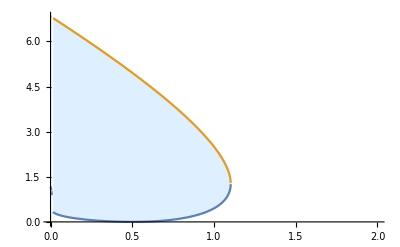

```mathematica
Plot[{p[η],q[η]},{η,0,2},Filling->{1->{{2},{LightBlue,White}}}]
```

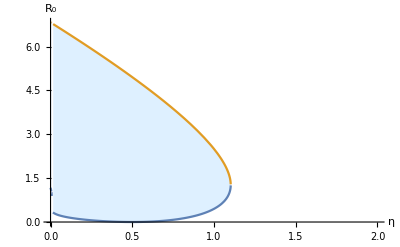

```mathematica
Show[%12,AxesLabel->{HoldForm[η],HoldForm[Subscript[R, 0]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["C:\\Users\\Roger Zhang\\Desktop\\0.5.pdf",%13,"PDF"]
```

C:\Users\Roger Zhang\Desktop\0.5.pdf